```mathematica
4.1数据拟合与插值

4.1.1数据拟合
```

```mathematica
Fit[data,funs,vars]对数据data用最小二乘法求函数表funs中各函数的一个线性组合作为所求的近似解析式,其中vars是自变量或自变量表
Fit[data,{1,x},x]求形为y=a+bx的近似式
Fit[data,{1,x,x^2},x]求形为y=a+bx+cx^2 的近似式
Fit[data,{1,x,y,xy},{x,y}]求形为z=a+bx+cy+dxy的近似式
```

```mathematica
例1:线性拟合
```

```mathematica
data={{19.1,76.3},{25,77.8},{30.1,79.25},{36,80.8},{40,82.35},{45.1,83.9},{50,85.1}};
f=Fit[data,{1,x},x]
```

```mathematica
pd=ListPlot[data];
fd=Plot[f,{x,19,52}];
Show[pd,fd]
```

```mathematica
例2:二次函数拟合
```

```mathematica
data={{0.1,5.1234},{0.2,5.3057},{0.3,5.5687},{0.4,5.9378},{0.5,6.4337},{0.6,7.0978},{0.7,7.9493},{0.8,9.0253},{0.9,10.3627}};
```

```mathematica
f=Fit[data,{1,x,x^2},x]
```

97.9105-1.626 x+0.00799184 x^2

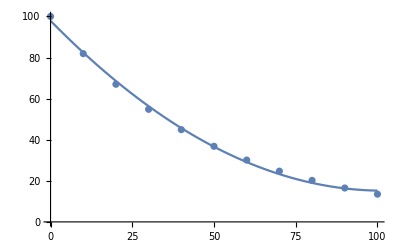

```mathematica
pd=ListPlot[data];
fd=Plot[f,{x,0,100}];
Show[pd,fd]
```

```mathematica
例3:二元函数拟合
```

```mathematica
Flatten[Table[{x,y,1+5x-x y},{x,0,1,0.2},{y,0,1,0.2}],1]
```

```mathematica
Fit[%,{1,x,y,x y},{x,y}]
```

```mathematica
Chop[%]
```

```mathematica
Chop[expr,δ]去掉表达式xepr的系数中绝对值小于δ的项,δ的默认值为10^-10
```

```mathematica
例4:使用初等函数的组合进行拟合
```

```mathematica
ft=Table[N[1+2Exp[-x/3]],{x,10}]
```

```mathematica
Fit[ft,{1,Sin[x],Exp[-x/3],Exp[-x]},x]
```

```mathematica
Chop[%]
```

```mathematica
4.1.2插值法构造近似函数
```

```mathematica
1.插值多项式
```

```mathematica
InterpolatingPolynomial[{f1,f2,...},x]当自变量的值为1,2,...时函数值为f1,f2,...
InterpolatingPolynomial[{{x1,y1},{x2,y2},...},x]当自变量的值为xi时函数值为yi
InterpolatingPolynomial[{x1,{f1,df1,ddf1,...},{x2,{f2,df2,ddf2,...}},...}x]
规定点xi 处的导数值
给定n+1个点,结果是n次多项式
Null
```

```mathematica
InterpolatingPolynomial[{1,-2,-1,1},x]
```

```mathematica
InterpolatingPolynomial[{{1,1},{3,-2},{5,-1},{7,1}},x]
```

```mathematica
InterpolatingPolynomial[{{1,{2,2,1}},{2,{2,3,4}}},x]
```

```mathematica
2.插值函数
```

```mathematica
(1)Interpolation
```

```mathematica
Interpolation[{f1,f2,,...},x]
当自变量的值为1,2,...时函数值为f1,f2,...
Interpolation[{{x1,y1},{x2,y2},...},x]
当自变量的值为xi时函数值为yi
Interpolation[{x1,{f1,df1,ddf1,...},{x2,{f2,df2,ddf2,...}},...}x]
规定点xi 处的导数值
如果构造多元函数 将参数改为:
{xi,yi,...fi}或{xi,yi,...{fi,{dxfi,fyfi,...}}}
```

```mathematica
可选参数
InterpolationOrder->n
```

```mathematica
返回结果为形如下式的插值函数
InterpolatingFunction[domain,table]
```

```mathematica
data={{0.1,5.1234},{0.2,5.3057},{0.3,5.5687},{0.4,5.9378},{0.5,6.4337},{0.6,7.0978},{0.7,7.9493},{0.8,9.0253},{0.9,10.3627}};
f=Interpolation[data]
```

```mathematica
pd=ListPlot[data,DisplayFunction->Identity];
fd=Plot[f[x],{x,0.1,0.9},DisplayFunction->Identity];
Show[pd,fd,DisplayFunction->$DisplayFunction]
```

```mathematica
f[0.2]
```

```mathematica
f[0.25]
```

```mathematica
f[0.3]
```

```mathematica
(2)ListInterpolation
由自变量取网格点时对应的函数值构造一个插值函数,使已知点处的近似函数的值等于已知值.
```

```mathematica
ListInterpolation[List,{{x1,x2,...},{y1,y2,..}}]
其中List是由网格点{xi,yi}对应的函数值组成的表
ListInterpolation[List,{{xmin,xmax},{ymin,ymax}}]
自变量取指定区间上的等分点
ListInterpolation[{{f11,f12,..},{f21,f22,..},..}]
只给出List,则自变量默认为取正整数.
```

```mathematica
f1=ListInterpolation[{{1.1,1.2,0.8},{0.2,0.9,0.5},{0.5,-0.7,1.4}},{{0,1,1.5},{-1,0,2}},InterpolationOrder->2]
```

```mathematica
f2=ListInterpolation[{{1.1,1.2,0.8},{0.2,0.9,0.5},{0.5,-0.7,1.4}},InterpolationOrder->2]
```

```mathematica
f1[1.5,0]
```

```mathematica
f2[3,2]
```

```mathematica
f1[1.3,1.1]
```

```mathematica
f2[2.3,2.1]
```

```mathematica
(3)FunctionInterpolation
由普通函数或已经存在的近似函数生成一个新的近似函数
```

```mathematica
FunctionInterpolation[expr,{x,xmin,xmax},{y,ymin,ymax}]
第一个参数是函数的表达式   后面的参数指定函数的定义域
```

```mathematica
data=Table[Sin[x-2y],{x,-2,2},{y,-2,2}]
f=ListInterpolation[data,{{-2,2},{-2,2}}]
```

```mathematica
g=FunctionInterpolation[f[Cos[2Pi t],Sin[2Pi t]],{t,0,1}]
```

```mathematica
Plot[{g[t],f[Cos[2Pi t],Sin[2Pi t]]},{t,0,1},PlotStyle->{RGBColor[1,0,0],RGBColor[0,0,1]}]
```